```mathematica
ClearAll["Global`*"]
```

```mathematica
(*
	Root System of Subscript[B, 2]

	Φ = {Subscript[α, 1], Subscript[α, 1]+Subscript[α, 2], Subscript[α, 1] + 2 Subscript[α, 2], Subscript[α, 2], -Subscript[α, 1], -(Subscript[α, 1]+Subscript[α, 2]), -(Subscript[α, 1] + 2 Subscript[α, 2]), -Subscript[α, 2]}

*)
```

```mathematica
Inverse[{{2,-2},{-1,2}}]
```

{{1,1},{1/2,1}}

```mathematica
Subscript[α, 1]={√2,0}; T={{Cos[3π/4],-Sin[3π/4]},{Sin[3π/4],Cos[3π/4]}};  
Subscript[α, 2]=(1/√2)(T.Subscript[α, 1]);a1=Subscript[α, 1]; a2=Subscript[α, 2];
```

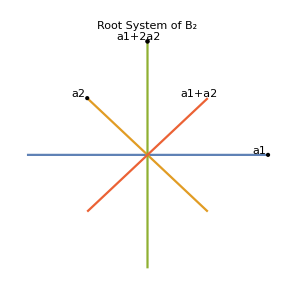

```mathematica
(* Plot the Root System of Subscript[B, 2] *)
origin = {0,0};
rootOrbit={{-Subscript[α, 1],Subscript[α, 1]},{-Subscript[α, 2],Subscript[α, 2]},{-(Subscript[α, 1] + 2 Subscript[α, 2]), Subscript[α, 1] + 2 Subscript[α, 2]}, {-(Subscript[α, 1] + Subscript[α, 2]), Subscript[α, 1] + Subscript[α, 2]}};
temp=ListLinePlot[rootOrbit,AspectRatio->Automatic,Axes->False,PlotLabel->Style["Root System of B_2",FontSize->12],Epilog->{Point[a1+2a2],Text["a1+2a2", a1+2a2+{-0.1,0.05}],Point[a1+2a2],Text["a1+a2", a1+a2+{-0.1,0.05}],Point[a2],Text["a2", a2+{-0.1,0.05}],Point[a1],Text["a1", a1+{-0.1,0.05}]}]
```

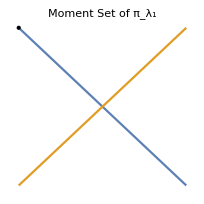

```mathematica
origin = {0,0};
rootOrbit2={{-Subscript[α, 2],Subscript[α, 2]}, {-(Subscript[α, 1] + Subscript[α, 2]), Subscript[α, 1] + Subscript[α, 2]}};
temp=ListLinePlot[rootOrbit2,AspectRatio->Automatic,Axes->False,PlotLabel->Style["Moment Set of π_λ_1",FontSize->12],Epilog->{Point[a1+2a2],Text["a1+a2", a1+a2+{-0.1,0.05}],Point[a2],Text["a2", a2+{0.1,0.05}]}]
```

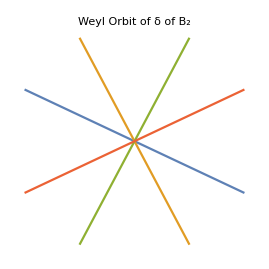

```mathematica
(*
	Let Subscript[W, Subscript[α, 1]], Subscript[W, Subscript[α, 2]] be the simple reflections, then the Weyl group 'W' of Subscript[B, 2] could contain such elements:
		
		W =  {e, Subscript[W, Subscript[α, 1]], Subscript[W, Subscript[α, 2]] Subscript[W, Subscript[α, 1]], Subscript[W, Subscript[α, 1]] Subscript[W, Subscript[α, 2]] Subscript[W, Subscript[α, 1]], Subscript[W, Subscript[α, 2]] Subscript[W, Subscript[α, 1]] Subscript[W, Subscript[α, 2]] Subscript[W, Subscript[α, 1]], Subscript[W, Subscript[α, 2]] Subscript[W, Subscript[α, 1]] Subscript[W, Subscript[α, 2]], Subscript[W, Subscript[α, 1]] Subscript[W, Subscript[α, 2]], Subscript[W, Subscript[α, 2]]}, and theirs signs are
          sign: +   -    +        -           +          -        +     -                ;

	The half sum of positives root: δ = 3/2 Subscript[α, 1] + 2 Subscript[α, 2]  , and the Weyl orbit of δ is

	{ 3/2 Subscript[α, 1] + 2 Subscript[α, 2] ,  1/2 Subscript[α, 1] + 2 Subscript[α, 2] ,  1/2 Subscript[α, 1] - Subscript[α, 2] , -3/2 Subscript[α, 1] - Subscript[α, 2], -3/2 Subscript[α, 1] - 2 Subscript[α, 2], -1/2 Subscript[α, 1] - 2 Subscript[α, 2] , -1/2 Subscript[α, 1] + Subscript[α, 2], 3/2 Subscript[α, 1] + Subscript[α, 2]}
*)

δ = 3/2 Subscript[α, 1] + 2 Subscript[α, 2];
deltaOrbitPlot={ {-1/2 Subscript[α, 1] + Subscript[α, 2], 1/2 Subscript[α, 1] - Subscript[α, 2]},{-1/2 Subscript[α, 1] - 2 Subscript[α, 2],1/2 Subscript[α, 1] + 2 Subscript[α, 2]},{-3/2 Subscript[α, 1] - 2 Subscript[α, 2],3/2 Subscript[α, 1] + 2 Subscript[α, 2]},{-3/2 Subscript[α, 1] - Subscript[α, 2], 3/2 Subscript[α, 1] +  Subscript[α, 2]}};
temp=ListLinePlot[deltaOrbitPlot,AspectRatio->Automatic,Axes->False,PlotLabel->Style["Weyl Orbit of δ of B_2",FontSize->12]]
```

```mathematica
(* Orbital projection measure of δ *)
scale=100; a1=Subscript[α, 1]; a2=Subscript[α, 2];
region=ParametricRegion[{t*a1[[1]]+s*(a1+a2)[[1]],t*a1[[2]]+s*(a1+a2)[[2]]},{{t,0,scale},{s,0,scale}}];
factor= 1/Det[Transpose[{a1,a1+a2}]];
f[x_,y_]:=factor*Piecewise[{{1, {x,y}∈region}},0];
g[x_,y_]=Integrate[f[x-t*(a1+2a2)[[1]],y-t*(a1+2a2)[[2]]],{t,0,scale}];
h[x_,y_]=Integrate[g[x-t*a2[[1]],y-t*a2[[2]]],{t,0,scale}];

deltaOrbit = {3/2 a1+ 2 a2 ,  1/2 a1 + 2 a2 ,  1/2 a1 - a2 , -3/2 a1 - a2, -3/2 a1 - 2 a2, -1/2 a1 - 2 a2 , -1/2 a1 + a2, 3/2 a1 + a2};
μ[x_,y_]:=∑_(i=1)^8 (-1)^(i+1)* h[deltaOrbit[[i,1]]-x,deltaOrbit[[i,2]]-y];
range=2.4;
data=Table[{x,y,If[μ[x,y]<=0.01,0,μ[x,y]]},{x,-range,range, 0.1},{y,-range,range,0.1}];
data1=Flatten[data,1];
(* temp=ListPointPlot3D[data1]; *)
ListPlot3D[data1,AspectRatio->Automatic,Axes->False,Boxed->False,Lighting->"Neutral",PlotRange->All,Mesh->{20},PlotLabel->Style["μ_δ^p",FontSize->12]]
```

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
(* calculate measure *)
```

```mathematica
(*define a basis for roots*)
a1={2,0};a2={0,2}; λ1=a1+a2;   H1 = {1,-1/2}; H2 = {-1,1};
```

```mathematica
(* weights of Subscript[λ, 1]
	{Subscript[λ, 1], Subscript[λ, 1]-Subscript[α, 1], 0, Subscript[λ, 1]-Subscript[α, 1]-2 Subscript[α, 2], Subscript[λ, 1]-2 Subscript[α, 1]-2 Subscript[α, 2]}
 *)
```

```mathematica
f[x_,y_]:=ⅇ^(ⅈ λ1.{x,y})/((-a1).{x,y}* (-λ1).{x,y}*(-a1-2a2).{x,y}*(-2a1-2a2).{x,y})+ⅇ^(ⅈ (λ1-a1).{x,y})/((a1).{x,y}* (-λ1+a1).{x,y}*(-2a2).{x,y}*(-a1-2a2).{x,y})+1/((λ1).{x,y}* (λ1-a1).{x,y}*(λ1-a1-2a2).{x,y}*(λ1-2a1-2a2).{x,y})+ⅇ^(ⅈ (λ1-a1-2a2).{x,y})/((a1+2a2).{x,y}* (2a2).{x,y}*(-λ1+a1+2a2).{x,y}*(-a1).{x,y})+ⅇ^(ⅈ (λ1-2a1-2a2).{x,y})/((2a1+2a2).{x,y}* (a1+2a2).{x,y}*(-λ1+2a1+2a2).{x,y}*(a1).{x,y});
```

```mathematica
h1*H1+h2*H2
```

{h1-h2,-h1/2+h2}

```mathematica
f[h1-h2,-h1/2+h2]//Simplify
```

```mathematica
(ⅇ^(-ⅈ (h1+2 h2)) (-ⅇ^(2 ⅈ h1) h1^2-ⅇ^(4 ⅈ h2) h1^2+ⅇ^(2 ⅈ h2) (h1-2 h2)^2+ⅇ^(2 ⅈ (h1+h2)) (h1-2 h2)^2+8 ⅇ^(ⅈ (h1+2 h2)) (h1-h2) h2))/(8 h1^2 (h1-2 h2)^2 (h1-h2) h2)//Expand
```

1/(h1 (h1-2 h2)^2 (h1-h2))-ⅇ^(2 ⅈ h2-ⅈ (h1+2 h2))/(2 h1 (h1-2 h2)^2 (h1-h2))-ⅇ^(2 ⅈ (h1+h2)-ⅈ (h1+2 h2))/(2 h1 (h1-2 h2)^2 (h1-h2))-ⅇ^(2 ⅈ h1-ⅈ (h1+2 h2))/(8 (h1-2 h2)^2 (h1-h2) h2)+ⅇ^(2 ⅈ h2-ⅈ (h1+2 h2))/(8 (h1-2 h2)^2 (h1-h2) h2)-ⅇ^(4 ⅈ h2-ⅈ (h1+2 h2))/(8 (h1-2 h2)^2 (h1-h2) h2)+ⅇ^(2 ⅈ (h1+h2)-ⅈ (h1+2 h2))/(8 (h1-2 h2)^2 (h1-h2) h2)-h2/(h1^2 (h1-2 h2)^2 (h1-h2))+(ⅇ^(2 ⅈ h2-ⅈ (h1+2 h2)) h2)/(2 h1^2 (h1-2 h2)^2 (h1-h2))+(ⅇ^(2 ⅈ (h1+h2)-ⅈ (h1+2 h2)) h2)/(2 h1^2 (h1-2 h2)^2 (h1-h2))

```mathematica
f0[h1_,h2_]:=(ⅇ^(-ⅈ (h1+2 h2)) (-ⅇ^(2 ⅈ h1) h1^2-ⅇ^(4 ⅈ h2) h1^2+ⅇ^(2 ⅈ h2) (h1-2 h2)^2+ⅇ^(2 ⅈ (h1+h2)) (h1-2 h2)^2+8 ⅇ^(ⅈ (h1+2 h2)) (h1-h2) h2))/(8 h1^2 (h1-2 h2)^2 (h1-h2) h2);
```

```mathematica
(h1 D[f0[h1,h2],h1]+h2 D[f0[h1,h2],h2])//Simplify
```

1/(8 h1^2 (h1-2 h2)^2 (h1-h2) h2)ⅇ^(-ⅈ (h1+2 h2)) (-ⅈ ⅇ^(2 ⅈ h2) (-4 ⅈ+h1) (h1-2 h2)^2+ⅈ ⅇ^(2 ⅈ (h1+h2)) (4 ⅈ+h1) (h1-2 h2)^2+ⅇ^(4 ⅈ h2) h1^2 (4+ⅈ h1-2 ⅈ h2)+ⅇ^(2 ⅈ h1) h1^2 (4-ⅈ h1+2 ⅈ h2)-32 ⅇ^(ⅈ (h1+2 h2)) (h1-h2) h2)

```mathematica
f1[h1_,h2_]:=1/(8 h1^2 (h1-2 h2)^2 (h1-h2) h2)ⅇ^(-ⅈ (h1+2 h2)) (-ⅈ ⅇ^(2 ⅈ h2) (-4 ⅈ+h1) (h1-2 h2)^2+ⅈ ⅇ^(2 ⅈ (h1+h2)) (4 ⅈ+h1) (h1-2 h2)^2+ⅇ^(4 ⅈ h2) h1^2 (4+ⅈ h1-2 ⅈ h2)+ⅇ^(2 ⅈ h1) h1^2 (4-ⅈ h1+2 ⅈ h2)-32 ⅇ^(ⅈ (h1+2 h2)) (h1-h2) h2);
```

```mathematica
(h1 D[f1[h1,h2],h1]+h2 D[f1[h1,h2],h2])//Simplify
```

1/(8 h1^2 (h1-2 h2)^2 (h1-h2) h2)ⅇ^(-ⅈ (h1+2 h2)) (-ⅇ^(2 ⅈ h2) (-16-7 ⅈ h1+h1^2) (h1-2 h2)^2-ⅇ^(2 ⅈ (h1+h2)) (-16+7 ⅈ h1+h1^2) (h1-2 h2)^2+128 ⅇ^(ⅈ (h1+2 h2)) (h1-h2) h2+ⅇ^(2 ⅈ h1) h1^2 (-16+7 ⅈ h1+h1^2-14 ⅈ h2-4 h1 h2+4 h2^2)+ⅇ^(4 ⅈ h2) h1^2 (-16-7 ⅈ h1+h1^2+14 ⅈ h2-4 h1 h2+4 h2^2))

```mathematica
f2[h1_,h2_]:=1/(8 h1^2 (h1-2 h2)^2 (h1-h2) h2)ⅇ^(-ⅈ (h1+2 h2)) (-ⅇ^(2 ⅈ h2) (-16-7 ⅈ h1+h1^2) (h1-2 h2)^2-ⅇ^(2 ⅈ (h1+h2)) (-16+7 ⅈ h1+h1^2) (h1-2 h2)^2+128 ⅇ^(ⅈ (h1+2 h2)) (h1-h2) h2+ⅇ^(2 ⅈ h1) h1^2 (-16+7 ⅈ h1+h1^2-14 ⅈ h2-4 h1 h2+4 h2^2)+ⅇ^(4 ⅈ h2) h1^2 (-16-7 ⅈ h1+h1^2+14 ⅈ h2-4 h1 h2+4 h2^2));
```

```mathematica
(h1 D[f2[h1,h2],h1]+h2 D[f2[h1,h2],h2])//FullSimplify
```

1/(8 h1^2 (h1-2 h2)^2 (h1-h2) h2)ⅇ^(-ⅈ (h1+2 h2)) (ⅇ^(2 ⅈ (h1+h2)) (-64+h1 (37 ⅈ+(9-ⅈ h1) h1)) (h1-2 h2)^2+ⅇ^(2 ⅈ h2) (-64+h1 (-37 ⅈ+(9+ⅈ h1) h1)) (h1-2 h2)^2-512 ⅇ^(ⅈ (h1+2 h2)) (h1-h2) h2-ⅈ ⅇ^(4 ⅈ h2) h1^2 (64 ⅈ+h1 (-37+h1 (-9 ⅈ+h1))+74 h2-6 h1 (-6 ⅈ+h1) h2+12 (-3 ⅈ+h1) h2^2-8 h2^3)+ⅈ ⅇ^(2 ⅈ h1) h1^2 (-64 ⅈ+h1 (-37+h1 (9 ⅈ+h1))+74 h2-6 h1 (6 ⅈ+h1) h2+12 (3 ⅈ+h1) h2^2-8 h2^3))

```mathematica
f3[h1_,h2_]:=1/(8 h1^2 (h1-2 h2)^2 (h1-h2) h2)ⅇ^(-ⅈ (h1+2 h2)) (ⅇ^(2 ⅈ (h1+h2)) (-64+h1 (37 ⅈ+(9-ⅈ h1) h1)) (h1-2 h2)^2+ⅇ^(2 ⅈ h2) (-64+h1 (-37 ⅈ+(9+ⅈ h1) h1)) (h1-2 h2)^2-512 ⅇ^(ⅈ (h1+2 h2)) (h1-h2) h2-ⅈ ⅇ^(4 ⅈ h2) h1^2 (64 ⅈ+h1 (-37+h1 (-9 ⅈ+h1))+74 h2-6 h1 (-6 ⅈ+h1) h2+12 (-3 ⅈ+h1) h2^2-8 h2^3)+ⅈ ⅇ^(2 ⅈ h1) h1^2 (-64 ⅈ+h1 (-37+h1 (9 ⅈ+h1))+74 h2-6 h1 (6 ⅈ+h1) h2+12 (3 ⅈ+h1) h2^2-8 h2^3));
```

```mathematica
(h1 D[f3[h1,h2],h1]+h2 D[f3[h1,h2],h2])//FullSimplify
```

1/(8 h1^2 (h1-2 h2)^2 (h1-h2) h2)ⅇ^(-ⅈ (h1+2 h2)) (ⅇ^(2 ⅈ h2) (256+h1 (175 ⅈ+h1 (-55+h1 (-10 ⅈ+h1)))) (h1-2 h2)^2+ⅇ^(2 ⅈ (h1+h2)) (256+h1 (-175 ⅈ+h1 (-55+h1 (10 ⅈ+h1)))) (h1-2 h2)^2+2048 ⅇ^(ⅈ (h1+2 h2)) (h1-h2) h2-ⅇ^(2 ⅈ h1) h1^2 (256+h1 (-175 ⅈ+h1 (-55+h1 (10 ⅈ+h1)))+350 ⅈ h2-4 h1 (-55+h1 (15 ⅈ+2 h1)) h2+4 (-55+6 h1 (5 ⅈ+h1)) h2^2-16 (5 ⅈ+2 h1) h2^3+16 h2^4)-ⅇ^(4 ⅈ h2) h1^2 (256+h1^4-2 h1^3 (5 ⅈ+4 h2)+h1^2 (-55+12 h2 (5 ⅈ+2 h2))+h1 (175 ⅈ-4 h2 (-55+30 ⅈ h2+8 h2^2))+2 h2 (-175 ⅈ+2 h2 (-55+4 h2 (5 ⅈ+h2)))))

```mathematica
f4[h1_,h2_]:=1/(8 h1^2 (h1-2 h2)^2 (h1-h2) h2)ⅇ^(-ⅈ (h1+2 h2)) (ⅇ^(2 ⅈ h2) (256+h1 (175 ⅈ+h1 (-55+h1 (-10 ⅈ+h1)))) (h1-2 h2)^2+ⅇ^(2 ⅈ (h1+h2)) (256+h1 (-175 ⅈ+h1 (-55+h1 (10 ⅈ+h1)))) (h1-2 h2)^2+2048 ⅇ^(ⅈ (h1+2 h2)) (h1-h2) h2-ⅇ^(2 ⅈ h1) h1^2 (256+h1 (-175 ⅈ+h1 (-55+h1 (10 ⅈ+h1)))+350 ⅈ h2-4 h1 (-55+h1 (15 ⅈ+2 h1)) h2+4 (-55+6 h1 (5 ⅈ+h1)) h2^2-16 (5 ⅈ+2 h1) h2^3+16 h2^4)-ⅇ^(4 ⅈ h2) h1^2 (256+h1^4-2 h1^3 (5 ⅈ+4 h2)+h1^2 (-55+12 h2 (5 ⅈ+2 h2))+h1 (175 ⅈ-4 h2 (-55+30 ⅈ h2+8 h2^2))+2 h2 (-175 ⅈ+2 h2 (-55+4 h2 (5 ⅈ+h2)))));
```

```mathematica
(* Trace of Subscript[dπ, Subscript[λ, 1]] and restrict to t 
	120+250 dγ+175 dγ^2+50 dγ^3+5 dγ^4+72 Subscript[h, 1]^2+42 dγ Subscript[h, 1]^2+6 dγ^2 Subscript[h, 1]^2+Subscript[h, 1]^4-144 Subscript[h, 1] Subscript[h, 2]-84 dγ Subscript[h, 1] Subscript[h, 2]-12 dγ^2 Subscript[h, 1] Subscript[h, 2]-4 Subscript[h, 1]^3 Subscript[h, 2]+144 Subscript[h, 2]^2+84 dγ Subscript[h, 2]^2+12 dγ^2 Subscript[h, 2]^2+4 Subscript[h, 1]^2 Subscript[h, 2]^2
*)
```

```mathematica
(* Calculate the character of  *)
120 *f0[h1,h2] + 250 * f1[h1,h2] + 175 *f2[h1,h2] + 50* f3[h1,h2] + 5 * f4[h1,h2] + 72 h1^2 * f0[h1,h2] + 42 * h1^2 * f1[h1,h2] + 6*h1^2 * f2[h1,h2]+h1^4*f0[h1,h2]-144 *h1*h2*f0[h1,h2]-84*h1*h2*f1[h1,h2]-12*h1*h2*f2[h1,h2]-4 h1^3*h2*f0[h1,h2]+144*h2^2*f0[h1,h2]+84*h2^2*f1[h1,h2]+12*h2^2*f2[h1,h2]+4*h1^2*h2^2*f0[h1,h2]//Simplify
```

1+ⅇ^(-ⅈ h1)+ⅇ^(ⅈ h1)+ⅇ^(-ⅈ (h1-2 h2))+ⅇ^(ⅈ (h1-2 h2))